```mathematica
elementList={"Sc"->1,"Ti"->2,"V"->3,"Cr"->4,"Mn"->5,"Fe"->6,"Co"->7,"Ni"->8,"Cu"->9,"Zn"->10,"Y"->11,"Zr"->12,"Nb"->13,"Mo"->14,"Tc"->15,"Ru"->16,"Rh"->17,"Pd"->18,"Ag"->19,"Hf"->20,"Ta"->21,"W"->22,"Re"->23,"Os"->24,"Ir"->25,"Pt"->26,"Au"->27};
elements=List@@@elementList//Transpose//First;
targets = {ORR -> -1.51, CORedCO -> -1.20, ORedCO -> -1.25};
```

## Parse Data:

```mathematica
data=Import["/home/marco/fridbDemo/allresults.json"];
```

Parse 38 atom NP oxygen binding energy:

```mathematica
atoms32=Select[data,StringCases[#[[1]],"32"]≠{}&];
atoms32Binding=Select[atoms32,StringCases[#[[1]],"Binding"]≠{}&];
dataall={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms32Binding)/.elementList;
tab=Table[Cases[dataall,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
smallBindingTable = Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;
```

Parse 79 atom NP oxygen:

```mathematica
atoms79=Select[data,StringCases[#[[1]],"60"]≠{}&];
atoms79Binding=Select[atoms79,StringCases[#[[1]],"Binding"]≠{}&];
dataall79={#[[1]],#[[2]],ToExpression[#[[3]]]}&/@({"M1","M2","result"}/.#[[2]]&/@atoms79Binding)/.elementList;
tab=Table[Cases[dataall79,{m,n,_}][[;;,3]],{m,1,27},{n,1,27}]//MatrixForm;
bigBindingTable = Table[With[{x=Cases[dataall79,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}];
Table[With[{x=Cases[dataall,{m,n,_}][[;;,3]]},If[x==={},0,x[[1]]]],{m,1,27},{n,1,27}]//MatrixForm;
```

## Make Matrix Plots:

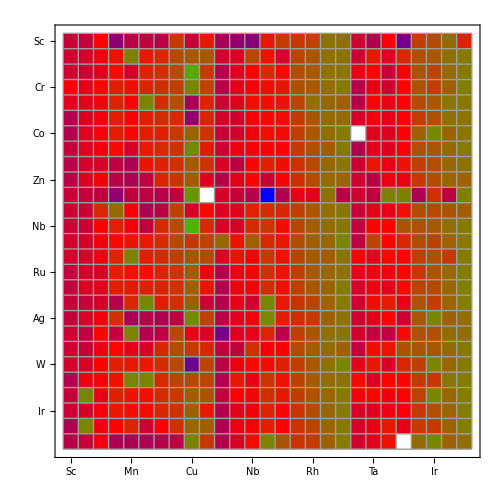

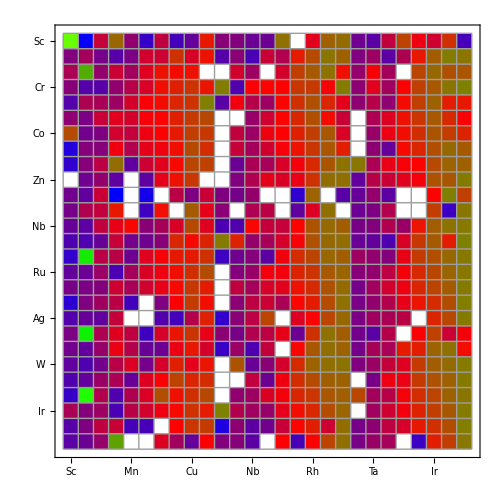

```mathematica
MatrixPlot[smallBindingTable,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]

MatrixPlot[bigBindingTable,ColorFunction->(Blend[{Blue,Red, Green, Yellow},#]&),ColorRules->{0->White},Mesh->True,Frame->True,FrameTicks->({#,#}&@Transpose@{Range@Length@elements,elements}),PlotRangePadding->None,ImageSize->500]
```

## Make Bar Charts:

### These statements are used to filter out spurious binding energies. Then nanoparticle removed has its corresponding label removed, so that the bar chart bars and their labes line up correctly

{{12}}

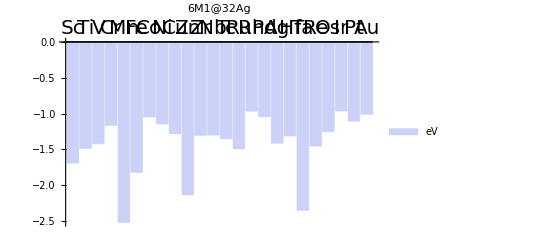

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

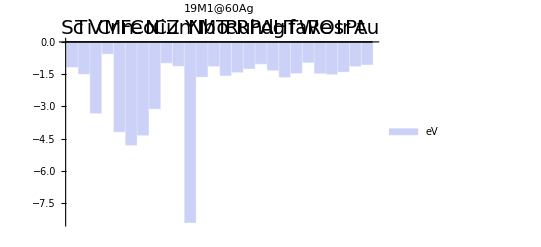

{{Sc},{Ti},{V},{Cr},{Mn},{Fe},{Co},{Ni},{Cu},{Zn},{Y},{Zr},{Nb},{Mo},{Tc},{Ru},{Rh},{Pd},{Ag},{Hf},{Ta},{W},{Re},{Os},{Ir},{Pt},{Au}}

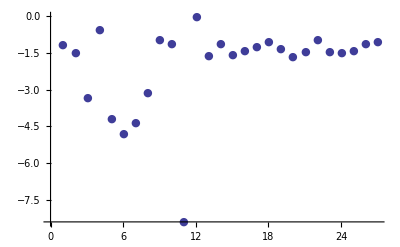

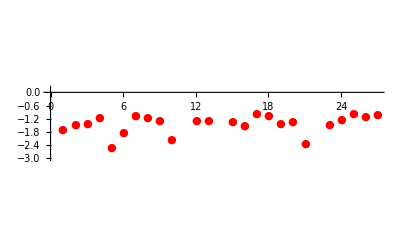

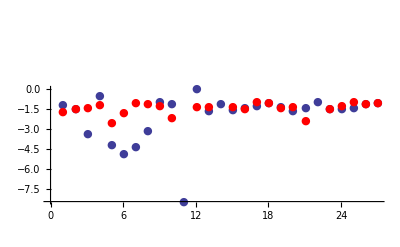

{0.528839,0.00008181,-1.8915,0.6229,-1.66226,-2.97975,-3.29121,-1.96083,0.313333,1.02347,1.6646,1.30394,-0.314616,-5.48928,-0.205317,0.0908144,-0.267932,0.0252885,0.100085,-0.317968,0.904503,-5.36616,0.00134848,-0.242626,-0.417037,-0.0155537,-0.0349103}

```mathematica
placeholder =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
removedElementsPos = Position[Map[ If[# >0 || # <-10 ,0,#] &,smallBindingTable[[All,19]] ],0];
newElementsSmall = Delete[elements, # & /@removedElementsPos] ;

placeholder2 =DeleteCases[Map[ If[# >0 || # <-10 ,0,#] &,bigBindingTable[[All,19]] ],0];
removedElementsPos2 = Position[Map[ If[# >0 || # <-10,0,#] &,bigBindingTable[[All,19]] ],0]
newElementsBig = Delete[elements, # & /@removedElementsPos2] ;
newElementsSmall == newElementsBig;
Delete[placeholder2, 1] ;

BarChart[placeholder,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsSmall,Above]},PlotLabel->Style["6M1@32Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements

BarChart[placeholder2,ChartLabels->{Placed[Style[#,FontSize->20]&/@newElementsBig,Above]},PlotLabel->Style["19M1@60Ag",Bold,50],ChartLegends->{"eV"}]
{#} & @@{#, Medium } & /@  elements
p1 = ListPlot[{#} & @bigBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}]


Show[p1,Graphics[{Red,elements}] ]
p2 = ListPlot[smallBindingTable[[All,19]], FillingStyle-> Thick, PlotMarkers -> {Automatic, Medium}, PlotStyle -> Red]
Show[p1,p2]
bigBindingTable[[All, 19]] - smallBindingTable[[All,19]]
```

## Ag, Pt Dot Chart

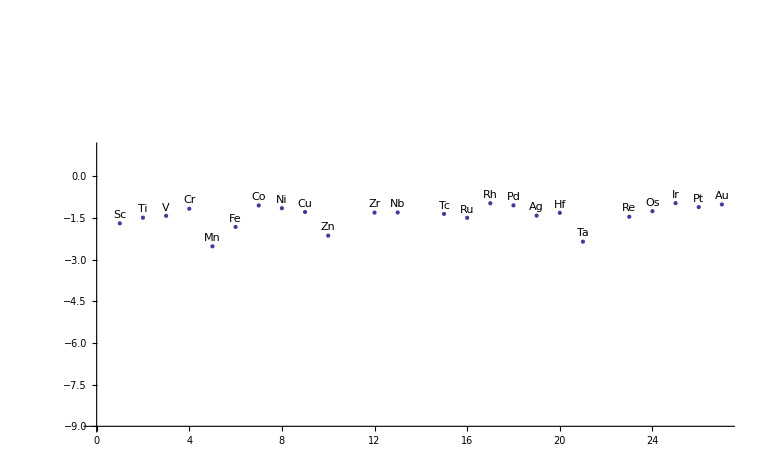

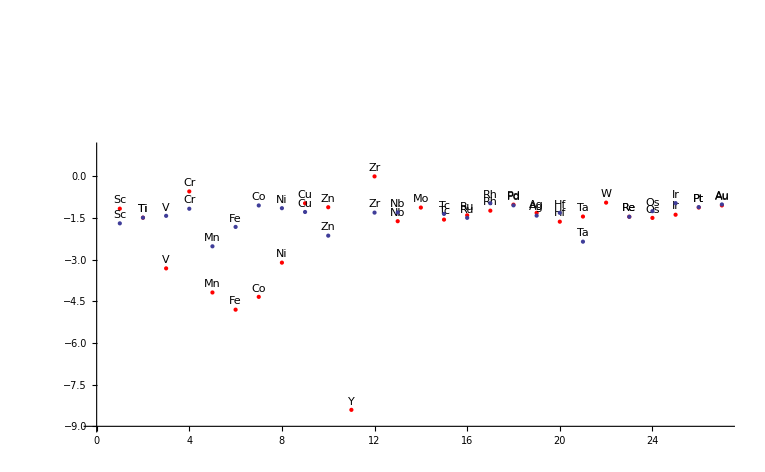

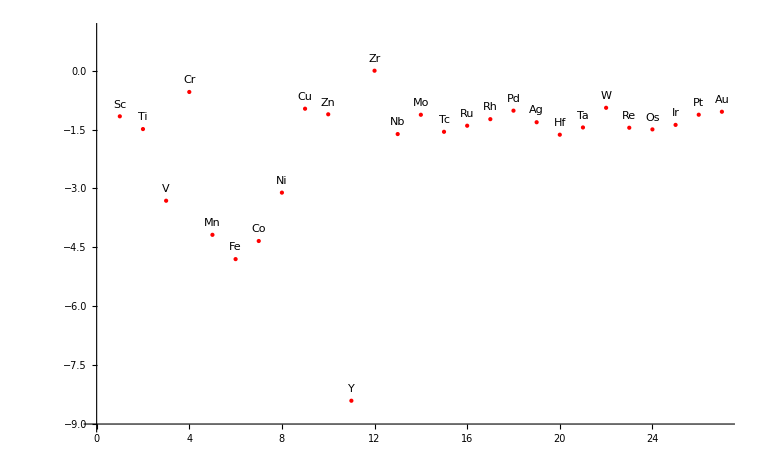

-Graphics-

```mathematica
dataPlot1=ListPlot[smallBindingTable[[All,19]],PlotStyle->PointSize->Large,AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}];
labels1=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@smallBindingTable[[All,19]]],smallBindingTable[[All,19]]}];
Show[dataPlot1,Graphics[labels1]]

dataPlot2=ListPlot[bigBindingTable[[All,19]],PlotStyle->{Red,PointSize->Large},AxesOrigin->{0,-9},PlotRange->{Automatic,{-9,1}}];
labels2=MapThread[Text[#1,{#2,#3+0.3}]&,{elements,Range[Length@bigBindingTable[[All,19]]],bigBindingTable[[All,19]]}];

Show[dataPlot2,Graphics[labels2], dataPlot1, Graphics[labels1]]
Show[dataPlot2,Graphics[labels2]]
Show[dataPlot1, Graphics[labels1]]
```

```mathematica
lst = Delete[lst,3]
```

{19→2.85077,27→2.8549,4→2.84034,9→2.81286,6→2.8282,20→2.96446,25→2.83727,5→2.83799,14→2.84114,13→2.91995,8→2.83038,24→2.84655,18→2.84554,26→2.84533,23→2.86048,17→2.84004,16→2.84042,1→2.92212,21→2.91318,15→2.85081,2→2.88824,3→2.87623,22→2.89723,11→2.96313,10→2.84196,12→2.97649}

## Average Bond Length Plots:

```mathematica
bondLenData = Import["/home/marco/fridbDemo/avgbondlen.json"] /. elementList;
```

Get Bond Length for bnp 38 nanoparticles

```mathematica
lst=  "bnp" /. bondLenData[[1]];
lst = "38" /. lst;

lst = Delete[lst,3];
lst = Delete[lst,8];
bnp38BL = Table[x, {x,1,27}] /. lst;
```

Get Bond Length for bnp 79 nanoparticles:

```mathematica
lst2=  "bnp" /. bondLenData[[1]];
lst2 = "79" /. lst2;
lst2 = Delete[lst,3];
lst2 = Delete[lst,8];
bnp79BL = Table[x, {x,1,27}] /. lst2; 

bondLenData[[1]]
```

bnp→{38→{19→2.85077,27→2.8549,Cd→2.88438,7→2.8297,4→2.84034,9→2.81286,6→2.8282,20→2.96446,Hg→2.87532,25→2.83727,5→2.83799,14→2.84114,13→2.91995,8→2.83038,24→2.84655,18→2.84554,26→2.84533,23→2.86048,17→2.84004,16→2.84042,1→2.92212,21→2.91318,15→2.85081,2→2.88824,3→2.87623,22→2.89723,11→2.96313,10→2.84196,12→2.97649},79→{19→2.87259,27→2.87463,Cd→2.88172,7→2.78466,4→2.82841,9→2.80938,6→2.77798,20→3.00874,25→2.81191,5→2.80125,14→2.82716,13→2.83941,8→2.7879,24→2.79815,18→2.82765,26→2.83002,23→2.8378,17→2.81816,16→2.80325,1→2.9742,21→2.96703,15→2.82528,2→2.8858,3→2.80727,22→2.83959,11→2.96012,10→2.85065}}

Make Plots of Bond Length data:

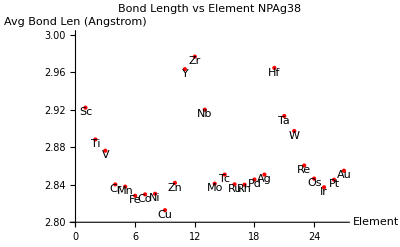

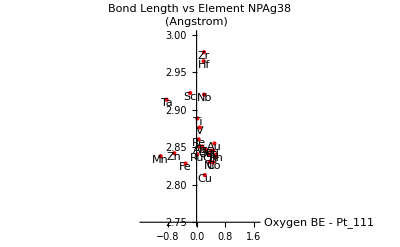

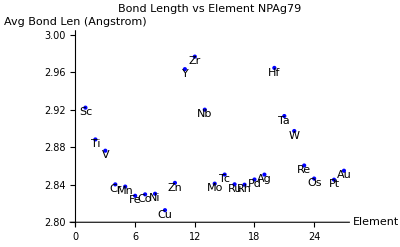

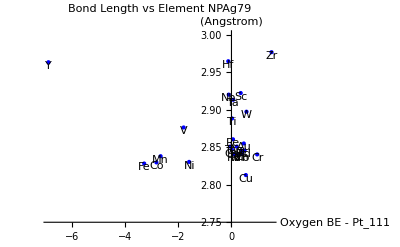

```mathematica
bondLenVsElement38 = ListPlot[bnp38BL, PlotStyle -> {Red, PointSize -> Large},PlotRange -> {2.80, 3},  PlotLabel -> "Bond Length vs Element NPAg38", AxesLabel->{"Element", "Avg Bond Len (Angstrom)"}];
bondLenVsElementLabels38=MapThread[Text[#1,{#2,#3-0.005}]&,{elements,Range[Length@bnp38BL], bnp38BL}];

bondLenVsBe38data = Partition[#,2] & @Riffle[#1, #2] & @@{smallBindingTable[[All,19]] - ORR /. targets, bnp38BL};
bondLenVsBe38=ListPlot[bondLenVsBe38data, PlotStyle->{Red,PointSize->Large}, PlotRange->{2.75, 3}, PlotLabel -> "Bond Length vs Element NPAg38", AxesLabel->{"Oxygen BE - Pt_111", "(Angstrom)"}];
bondLenVsBeLabels38=MapThread[Text[#1,{#2 ,#3- 0.005}]&,{elements,smallBindingTable[[All,19]] - ORR /. targets, bnp38BL}];

bondLenVsElement79 = ListPlot[bnp79BL, PlotStyle -> {Blue, PointSize -> Large},PlotRange -> {2.80, 3},  PlotLabel -> "Bond Length vs Element NPAg79", AxesLabel->{"Element", "Avg Bond Len (Angstrom)"}];
bondLenVsElementLabels79=MapThread[Text[#1,{#2,#3-0.005}]&,{elements,Range[Length@bnp79BL], bnp79BL}];

bondLenVsBe79data = Partition[#,2] & @Riffle[#1, #2] & @@{bigBindingTable[[All,19]] - ORR /. targets, bnp79BL};
bondLenVsBe79=ListPlot[bondLenVsBe79data, PlotStyle->{Blue,PointSize->Large}, PlotRange->{2.75, 3}, PlotLabel -> "Bond Length vs Element NPAg79", AxesLabel->{"Oxygen BE - Pt_111", "(Angstrom)"}];
bondLenVsBeLabels79=MapThread[Text[#1,{#2 ,#3- 0.005}]&,{elements,bigBindingTable[[All,19]] - ORR /. targets, bnp79BL}];




Show[bondLenVsElement38, Graphics[bondLenVsElementLabels38] ]
Show[bondLenVsBe38, Graphics[bondLenVsBeLabels38] ]

Show[bondLenVsElement79, Graphics[bondLenVsElementLabels79] ]
Show[bondLenVsBe79, Graphics[bondLenVsBeLabels79] ]
```

## Filter Particles:

```mathematica
idealORRSmall = Replace[smallBindingTable- (ORR) /. targets,a_/;Abs[a]≥0.05->0,{2}] ;
idealORRBig = Replace[bigBindingTable- (ORR) /. targets ,a_/;Abs[a] ≥0.05->0,{2}];
```

```mathematica
info[tbl_]:=With[{s=SparseArray[tbl]},ArrayPad[Append@@@Transpose[{s["NonzeroPositions"],s["NonzeroValues"]}],{0,{1,0}},ToString@Unevaluated@tbl]]

SetAttributes[info,HoldFirst]
MapAt[info,Replace[bigBindingTable- (ORR) /. targets ,a_/;Abs[a] ≥0.05->0,{2}],3]

info[idealORRSmall]/.  Reverse /@ elementList;
info[idealORRBig] /.  Reverse /@ elementList;
```

ArrayPad::depth: Padding amount {0, {1, 0}} should specify padding in no more than the number of dimensions in array {}.

### Filter For Tunable Particles:

```mathematica
coord = {1,2,3}
# == 2& /@ coord
```

{1,2,3}

{False,True,False}

{{1,2,3}}

## Final Figures:

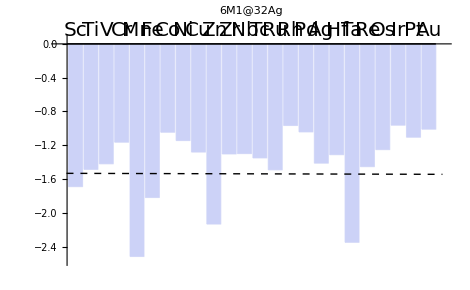
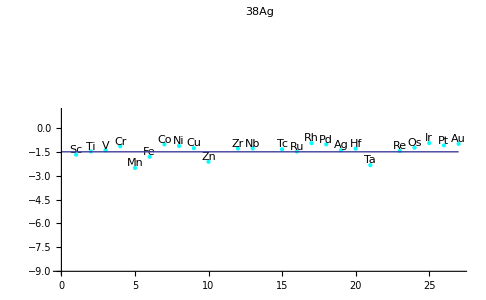
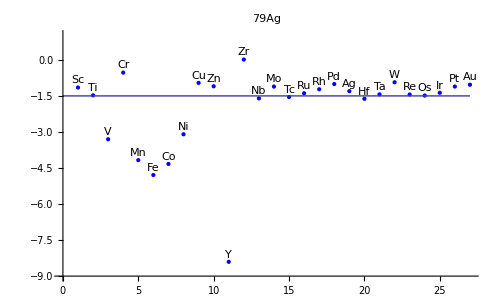
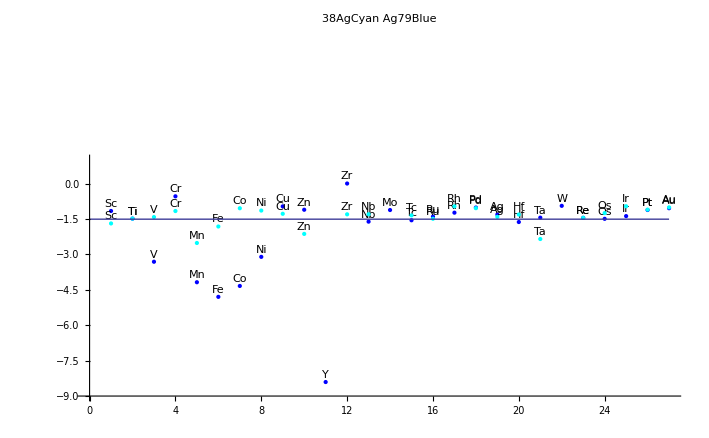
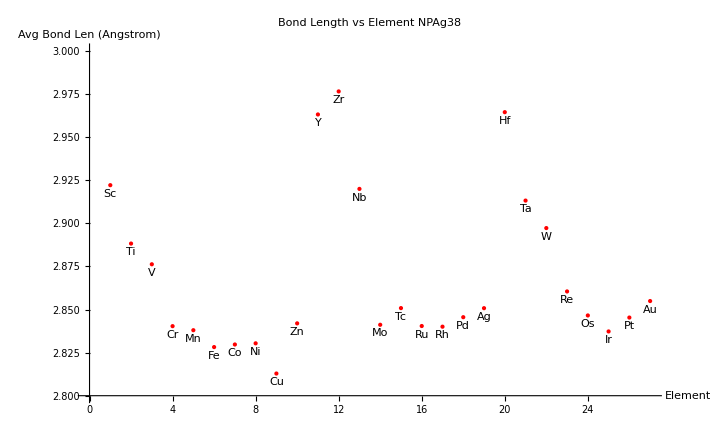
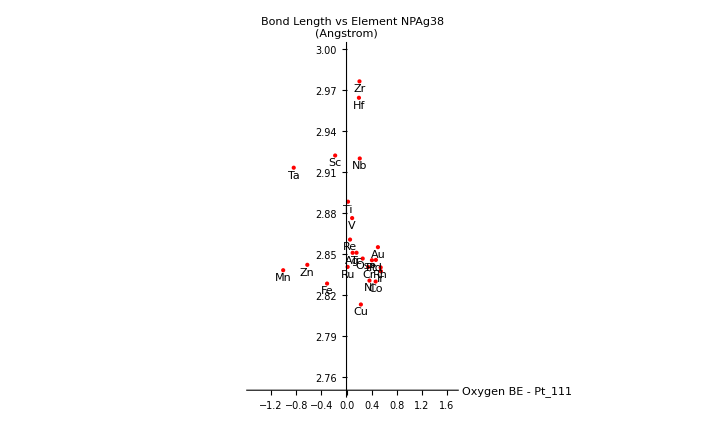
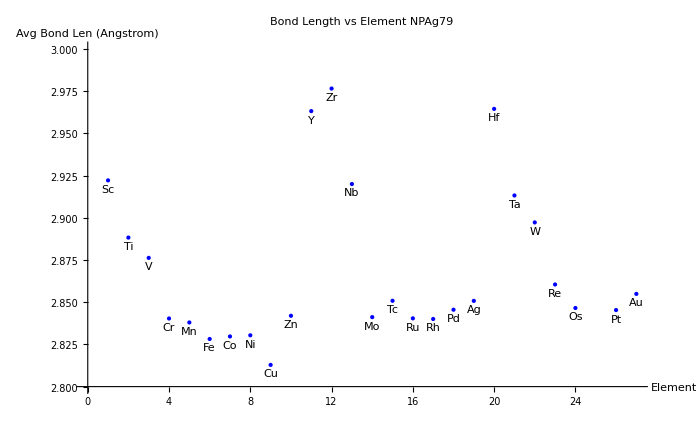
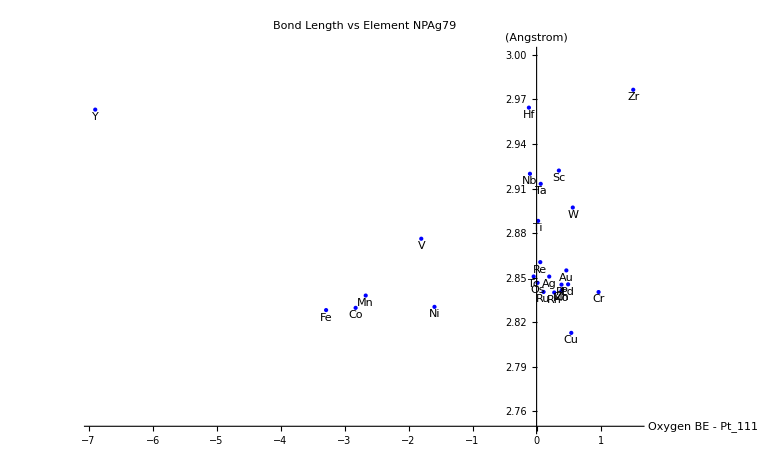
```mathematica
Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-
```

Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-

```mathematica
Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics-
```

Figures I want to keep:
-Graphics-
-Graphics--Graphics-
-Graphics-

-Graphics--Graphics-

-Graphics-

```mathematica
stackTest = {{1,2,3,4,5,6,7,8,9,10}}
```

{{1,2,3,4,5,6,7,8,9,10}}

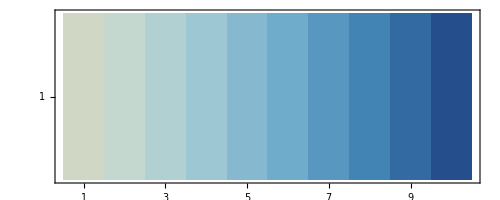

```mathematica
MatrixPlot[stackTest, ColorFunction->"RedBlueTones"]
```

```mathematica
Length[tunableORRData]
```

27

```mathematica
smallBindingTable
```

```mathematica
Function[myTable, {tunableORRData = Replace[myTable ,a_/;Abs[a]≥10->0,{2}] - ORR /. targets;d=Sign@Diagonal@tunableORRData; returnValue[row_, col_,myTable] := myTable[[row,col]] ;tunablePairs = Position[(tunableORRDataᵀ d)ᵀ,_?Negative]  /. Reverse /@ elementList; pairEnergy = returnValue[#1, #2]& @@{#1,#2}&@@@Position[(tunableORRDataᵀ d)ᵀ,_?Negative] ;
tempVar = Partition[Riffle[tunablePairs, pairEnergy],2];
filterImposs = Replace[tempVar,a_/;Abs[a]≥5->0 ,{2}] ;
filterImposs = Replace[filterImposs,a_/;a > 1->0 ,{2}] ;
Cases[filterImposs,{x_,y_}/;y ≠ 0]}][#] & /@ {smallBindingTable, bigBindingTable}








(*Cases[tt,x_/;Abs[x[[1]]-x[[2]]]>3];*)
```

{{{{{Sc,Pd},-1.47187},{{Sc,Ag},-1.69071},{{Ti,Mn},0.860106},{{Ti,Au},-1.19295},{{V,Au},-1.10513},{{Cr,Au},-0.131714},{{Mn,Ag},-2.51796},{{Mn,Pt},-1.29537},{{Mn,Au},-1.21843},{{Fe,Ag},-1.81939},{{Fe,Au},-1.44088},{{Co,Au},-1.30395},{{Ni,Au},-0.671956},{{Zn,Ag},-2.13397},{{Y,W},-0.189288},{{Nb,Au},-1.087},{{Mo,Au},-1.1764},{{Tc,Au},-0.922638},{{Ru,Au},-0.787955},{{Rh,Au},-0.482705},{{Pd,Au},-0.379127},{{Ta,Ag},-2.3501},{{Ta,Au},-1.12029},{{W,Au},-1.16135},{{Re,Pt},-1.22974},{{Re,Au},-1.04512},{{Os,Au},-0.76104},{{Ir,Au},-0.578992},{{Pt,Au},-0.593863}}},{{{{Sc,Ni},-3.41948},{{Sc,Zn},-4.47385},{{Sc,Tc},-3.34368},{{Sc,Ru},-3.56681},{{Ti,Zn},-2.80093},{{Ti,Nb},-3.18594},{{Ti,Pd},-1.61127},{{Ti,Pt},-1.63843},{{V,Mo},-3.96864},{{V,Pd},-1.60509},{{V,Ag},-1.42055},{{V,Ir},-3.26455},{{V,Au},-1.10513},{{Cr,Zn},-3.2243},{{Cr,Pt},-2.29656},{{Mn,Ag},-2.51796},{{Mn,Ir},-2.71754},{{Mn,Au},-1.21843},{{Fe,Zn},-4.12367},{{Fe,Ag},-1.81939},{{Fe,Au},-1.44088},{{Co,Zn},-3.61848},{{Co,Ag},-1.04659},{{Co,Au},-1.30395},{{Ni,Zn},-4.38025},{{Ni,Ag},-1.14478},{{Ni,Pt},-2.00655},{{Ni,Au},-0.671956},{{Cu,Zn},-3.60933},{{Cu,Pt},-2.07835},{{Zn,Pd},-1.87809},{{Y,Pd},-1.56194},{{Zr,Ni},-3.28998},{{Zr,Zn},-4.81045},{{Zr,Tc},-4.14224},{{Zr,Pd},-1.60735},{{Zr,Re},-4.66692},{{Zr,Os},-3.10247},{{Zr,Pt},-2.96714},{{Nb,Zn},-3.93171},{{Nb,Pd},-1.65592},{{Nb,Ag},-1.29924},{{Nb,Pt},-1.77984},{{Mo,Zn},-3.30349},{{Mo,Y},-1.99753},{{Mo,Zr},-4.60329},{{Mo,Pd},-1.92627},{{Tc,Zn},-3.15032},{{Tc,Zr},-4.66455},{{Tc,Pd},-2.46921},{{Tc,Ag},-1.35072},{{Tc,Pt},-3.48518},{{Ru,Cr},-4.23323},{{Ru,Pt},-2.03626},{{Rh,Zn},-4.57655},{{Pd,Mn},-4.13434},{{Ag,Zn},-3.30866},{{Ag,Tc},-4.29201},{{Ag,Os},-2.8647},{{Hf,Pd},-1.62158},{{Hf,Ag},-1.31235},{{Hf,Re},-4.86036},{{Hf,Au},-1.63271},{{Ta,Zn},-4.04648},{{Ta,Nb},-3.66082},{{Ta,Pd},-1.66047},{{Ta,Ir},-2.83783},{{Ta,Pt},-1.80795},{{Ta,Au},-1.12029},{{W,Zn},-3.26868},{{W,Rh},-2.7658},{{W,Pd},-1.52766},{{W,Pt},-2.01085},{{Re,Zn},-3.20482},{{Re,Hf},-4.80219},{{Re,Pt},-1.22974},{{Os,Cr},-4.26711},{{Os,Zn},-2.97908},{{Os,Pt},-2.06396},{{Ir,Cr},-4.53383},{{Ir,Zn},-4.46419},{{Pt,Mn},-4.17768},{{Pt,Zn},-2.38308},{{Au,Zn},-3.50652},{{Au,Ru},-3.79717},{{Au,Os},-1.87671}}}}

```mathematica
tst = { {1,2,3}, {2,3,4}, {4,5,6} }
```

{{1,2,3},{2,3,4},{4,5,6}}

```mathematica
tst[[All,1]]
tst[[All,2]]
```

{1,2,4}

```mathematica
{2,3,5}
```

{2,3,5}

```mathematica
L[#]& @@{1}
```

L[1]

```mathematica
(256.4 + 25 + 75)/(35*4 + 20 + 40 + 35 + 60 + 25 + 80)
```

0.891

(({Sc,Ni}
-3.41948) | ({Sc,Zn}
-4.47385) | ({Sc,Tc}
-3.34368) | ({Sc,Ru}
-3.56681) | ({Ti,Zn}
-2.80093) | ({Ti,Nb}
-3.18594) | ({Ti,Pd}
-1.61127) | ({Ti,Pt}
-1.63843) | ({V,Mo}
-3.96864) | ({V,Pd}
-1.60509) | ({V,Ag}
-1.42055) | ({V,Ir}
-3.26455) | ({V,Au}
-1.10513) | ({Cr,Zn}
-3.2243) | ({Cr,Pt}
-2.29656) | ({Mn,Ag}
-2.51796) | ({Mn,Ir}
-2.71754) | ({Mn,Au}
-1.21843) | ({Fe,Zn}
-4.12367) | ({Fe,Ag}
-1.81939) | ({Fe,Au}
-1.44088) | ({Co,Zn}
-3.61848) | ({Co,Ag}
-1.04659) | ({Co,Au}
-1.30395) | ({Ni,Zn}
-4.38025) | ({Ni,Ag}
-1.14478) | ({Ni,Pt}
-2.00655) | ({Ni,Au}
-0.671956) | ({Cu,Zn}
-3.60933) | ({Cu,Pt}
-2.07835) | ({Zn,Pd}
-1.87809) | ({Y,Pd}
-1.56194) | ({Zr,Ni}
-3.28998) | ({Zr,Zn}
-4.81045) | ({Zr,Tc}
-4.14224) | ({Zr,Pd}
-1.60735) | ({Zr,Re}
-4.66692) | ({Zr,Os}
-3.10247) | ({Zr,Pt}
-2.96714) | ({Nb,Zn}
-3.93171) | ({Nb,Pd}
-1.65592) | ({Nb,Ag}
-1.29924) | ({Nb,Pt}
-1.77984) | ({Mo,Zn}
-3.30349) | ({Mo,Y}
-1.99753) | ({Mo,Zr}
-4.60329) | ({Mo,Pd}
-1.92627) | ({Tc,Zn}
-3.15032) | ({Tc,Zr}
-4.66455) | ({Tc,Pd}
-2.46921) | ({Tc,Ag}
-1.35072) | ({Tc,Pt}
-3.48518) | ({Ru,Cr}
-4.23323) | ({Ru,Pt}
-2.03626) | ({Rh,Zn}
-4.57655) | ({Pd,Mn}
-4.13434) | ({Ag,Zn}
-3.30866) | ({Ag,Tc}
-4.29201) | ({Ag,Os}
-2.8647) | ({Hf,Pd}
-1.62158) | ({Hf,Ag}
-1.31235) | ({Hf,Re}
-4.86036) | ({Hf,Au}
-1.63271) | ({Ta,Zn}
-4.04648) | ({Ta,Nb}
-3.66082) | ({Ta,Pd}
-1.66047) | ({Ta,Ir}
-2.83783) | ({Ta,Pt}
-1.80795) | ({Ta,Au}
-1.12029) | ({W,Zn}
-3.26868) | ({W,Rh}
-2.7658) | ({W,Pd}
-1.52766) | ({W,Pt}
-2.01085) | ({Re,Zn}
-3.20482) | ({Re,Hf}
-4.80219) | ({Re,Pt}
-1.22974) | ({Os,Cr}
-4.26711) | ({Os,Zn}
-2.97908) | ({Os,Pt}
-2.06396) | ({Ir,Cr}
-4.53383) | ({Ir,Zn}
-4.46419) | ({Pt,Mn}
-4.17768) | ({Pt,Zn}
-2.38308) | ({Au,Zn}
-3.50652) | ({Au,Ru}
-3.79717) | ({Au,Os}
-1.87671))

filterTunable[tables]
h[{#1, #2} & @@ filterTunable[tables]];

```mathematica
{one, two} = filterTunable[tables];
preProcTunable[one]
```

Part::partd: Part specification "Sc" ⟦ 2 ⟧ is longer than depth of object.

Part::partd: Part specification 1 ⟦ 2 ⟧ is longer than depth of object.

Part::pspec: Part specification 1 ⟦ 2 ⟧ is neither a machine-sized integer nor a list of machine-sized integers.

Part::pspec: Part specification -1.47187 is neither a machine-sized integer nor a list of machine-sized integers.

Append::normal: Nonatomic expression expected at position 1 in Append[-1.47187, {{{"Sc", "Pd"}, -1.47187}, {{"Sc", "Ag"}, -1.69071}, {{"Ti", "Mn"}, 0.860106}, {{"Ti", "Au"}, -1.19295}, {{"V", "Au"}, -1.10513}, {{"Cr", "Au"}, -0.131714}, {{"Mn", "Ag"}, -2.51796}, {{"Mn", "Pt"}, -1.29537}, « 13 », {{"Ta", "Ag"}, -2.3501}, {{"Ta", "Au"}, -1.12029}, {{"W", "Au"}, -1.16135}, {{"Re", "Pt"}, -1.22974}, {{"Re", "Au"}, -1.04512}, {{"Os", "Au"}, -0.76104}, {{"Ir", "Au"}, -0.578992}, {{"Pt", "Au"}, -0.593863}} ⟦ -1.47187, -1.47187 ⟧].

{{{{Sc,Pd,{{{Sc,Pd},-1.47187},{{Sc,Ag},-1.69071},{{Ti,Mn},0.860106},{{Ti,Au},-1.19295},{{V,Au},-1.10513},{{Cr,Au},-0.131714},{{Mn,Ag},-2.51796},{{Mn,Pt},-1.29537},{{Mn,Au},-1.21843},{{Fe,Ag},-1.81939},{{Fe,Au},-1.44088},{{Co,Au},-1.30395},{{Ni,Au},-0.671956},{{Zn,Ag},-2.13397},{{Y,W},-0.189288},{{Nb,Au},-1.087},{{Mo,Au},-1.1764},{{Tc,Au},-0.922638},{{Ru,Au},-0.787955},{{Rh,Au},-0.482705},{{Pd,Au},-0.379127},{{Ta,Ag},-2.3501},{{Ta,Au},-1.12029},{{W,Au},-1.16135},{{Re,Pt},-1.22974},{{Re,Au},-1.04512},{{Os,Au},-0.76104},{{Ir,Au},-0.578992},{{Pt,Au},-0.593863}}⟦1⟦2⟧,1⟦2⟧⟧},Append[-1.47187,{{{Sc,Pd},-1.47187},{{Sc,Ag},-1.69071},{{Ti,Mn},0.860106},{{Ti,Au},-1.19295},{{V,Au},-1.10513},{{Cr,Au},-0.131714},{{Mn,Ag},-2.51796},{{Mn,Pt},-1.29537},{{Mn,Au},-1.21843},{{Fe,Ag},-1.81939},{{Fe,Au},-1.44088},{{Co,Au},-1.30395},{{Ni,Au},-0.671956},{{Zn,Ag},-2.13397},{{Y,W},-0.189288},{{Nb,Au},-1.087},{{Mo,Au},-1.1764},{{Tc,Au},-0.922638},{{Ru,Au},-0.787955},{{Rh,Au},-0.482705},{{Pd,Au},-0.379127},{{Ta,Ag},-2.3501},{{Ta,Au},-1.12029},{{W,Au},-1.16135},{{Re,Pt},-1.22974},{{Re,Au},-1.04512},{{Os,Au},-0.76104},{{Ir,Au},-0.578992},{{Pt,Au},-0.593863}}⟦-1.47187,-1.47187⟧]}}}

```mathematica
small[[1, All, 1,2]]
tst =  smallBindingTable[[#,#]] & /@ Flatten[small[[1,All,1,2]] /. elementList]
```

{Pd,Ag,Mn,Au,Au,Au,Ag,Pt,Au,Ag,Au,Au,Au,Ag,W,Au,Au,Au,Au,Au,Au,Ag,Au,Au,Pt,Au,Au,Au,Au}

{-2.21809,-1.41273,-4.97377,-1.69444,-1.69444,-1.69444,-1.41273,-2.25102,-1.69444,-1.41273,-1.69444,-1.69444,-1.69444,-1.41273,-6.11537,-1.69444,-1.69444,-1.69444,-1.69444,-1.69444,-1.69444,-1.41273,-1.69444,-1.69444,-2.25102,-1.69444,-1.69444,-1.69444,-1.69444}

```mathematica
tst
```

{-2.21809,-1.41273,-4.97377,-1.69444,-1.69444,-1.69444,-1.41273,-2.25102,-1.69444,-1.41273,-1.69444,-1.69444,-1.69444,-1.41273,-6.11537,-1.69444,-1.69444,-1.69444,-1.69444,-1.69444,-1.69444,-1.41273,-1.69444,-1.69444,-2.25102,-1.69444,-1.69444,-1.69444,-1.69444}

```mathematica
h @@@ {{ hi, bye}, {no,no}}
```

{h[hi,bye],h[no,no]}